```mathematica
Quit[]
```

1

Piecewise[{{-1-2 u, u<-1}, {u^2, -1<u<1}, {-1+2 u, u≥1}, {2, True}}]

Piecewise[{{-2, u<-1}, {2, u≥1}, {2 u, -1<u<1}, {Indeterminate, True}}]

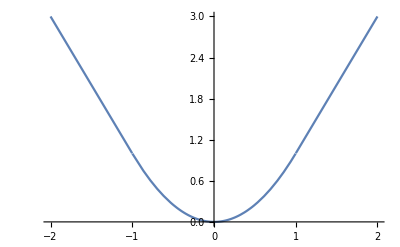

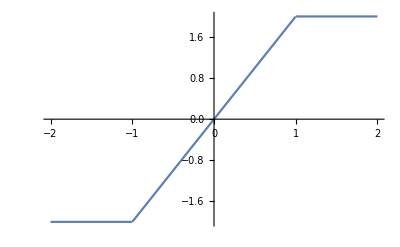

2 Sign[u] (UnitStep[-1-u]+UnitStep[-1+u])+2 u (-UnitStep[-1+u]+UnitStep[1+u])

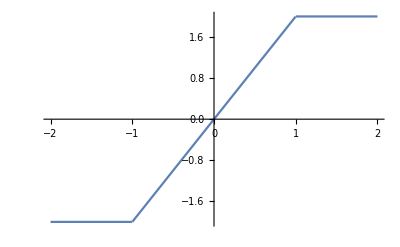

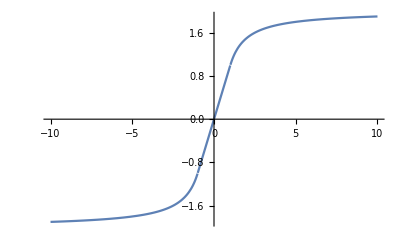

```mathematica
t=1
f[u_]=FullSimplify[u^2*(UnitStep[u+t]-UnitStep[u-t])+t*(2*Abs[u]-t)*(UnitStep[-u-t]+UnitStep[u-t])]
df[u_]=FullSimplify[D[f[u],u]]
Plot[f[u],{u,-2,2}]
Plot[df[u],{u,-2,2}]
g[u_]=2u*(UnitStep[u+t]-UnitStep[u-t])+2*t*Sign[u]*(UnitStep[-u-t]+UnitStep[u-t])
Plot[g[u],{u,-2,2}]
Plot[f[u]/u,{u,-10,10}]
```

1

(-1+Abs[u]) (UnitStep[-1-u]+UnitStep[-1+u])

Piecewise[{{Sign[u], u>1||u<-1}, {0, -1<u<1}, {Indeterminate, True}}]

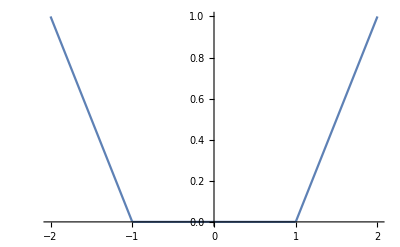

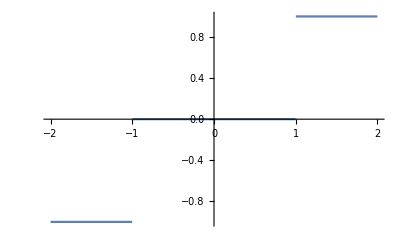

((-1+Abs[u]) (UnitStep[-1-u]+UnitStep[-1+u]))/u

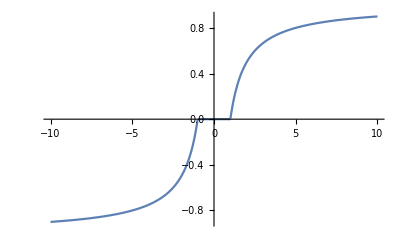

```mathematica
t=1
f[u_]=FullSimplify[0*(UnitStep[u+t]-UnitStep[u-t])+(Abs[u]-t)*(UnitStep[-u-t]+UnitStep[u-t])]
df[u_]=FullSimplify[D[f[u],u]]
Plot[f[u],{u,-2,2}]
Plot[df[u],{u,-2,2}]
g[u_]=FullSimplify[f[u]/u]
Plot[g[u],{u,-10,10}]
```

1

(-1+Abs[u]) (UnitStep[-1-u]+UnitStep[-1+u])

((-1+Abs[u]) (UnitStep[-1-u]+UnitStep[-1+u]))/u

Piecewise[{{1/u^2, u>1||u<-1}, {0, -1<u<1}, {Indeterminate, True}}]

Piecewise[{{-2/u^3, u>1||u<-1}, {0, -1<u<1}, {Indeterminate, True}}]

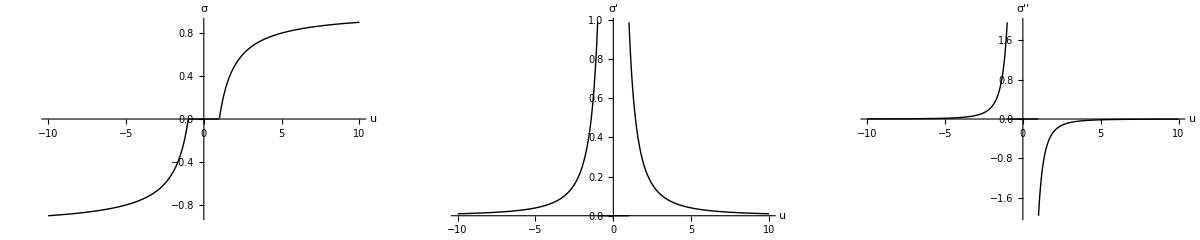

```mathematica
t=1
f[u_]=FullSimplify[0*(UnitStep[u+t]-UnitStep[u-t])+(Abs[u]-t)*(UnitStep[-u-t]+UnitStep[u-t])]
σ[u_]=FullSimplify[f[u]/u]
dσ[u_]=FullSimplify[D[σ[u],u]]
ddσ[u_]=FullSimplify[D[dσ[u],u]]
p1=Plot[σ[u],{u,-10,10},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Black,Thick},Ticks->None,AxesLabel->{u,"σ"}];
p2=Plot[dσ[u],{u,-10,10},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Black,Thick},Ticks->None,AxesLabel->{u,"σ'"}];
p3=Plot[ddσ[u],{u,-10,10},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Black,Thick},Ticks->None,AxesLabel->{u,"σ''"}];
GraphicsGrid[{{p1,p2,p3}}]
```

```mathematica
Quit[]
```

1

Piecewise[{{-1-2 u, u<-1}, {u^2, -1<u<1}, {-1+2 u, u≥1}, {2, True}}]

Piecewise[{{-1-2 u, u<-1}, {u^2, -1<u<1}, {-1+2 u, u≥1}, {2, True}}]/(2 u)

Piecewise[{{1/2, -1<u<1}, {1/(2 u^2), u≥1||u<-1}, {Indeterminate, True}}]

Piecewise[{{-1/u^3, u>1||u<-1}, {0, -1<u<1}, {Indeterminate, True}}]

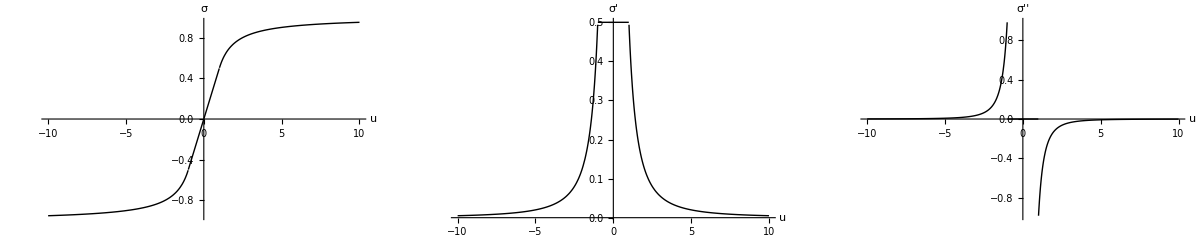

```mathematica
t=1
f[u_]=FullSimplify[u^2*(UnitStep[u+t]-UnitStep[u-t])+t*(2*Abs[u]-t)*(UnitStep[-u-t]+UnitStep[u-t])]
σ[u_]=FullSimplify[f[u]/(2u)]
dσ[u_]=FullSimplify[D[σ[u],u]]
ddσ[u_]=FullSimplify[D[dσ[u],u]]
p1=Plot[σ[u],{u,-10,10},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Black,Thick},Ticks->None,AxesLabel->{u,"σ"}];
p2=Plot[dσ[u],{u,-10,10},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Black,Thick},Ticks->None,AxesLabel->{u,"σ'"}];
p3=Plot[ddσ[u],{u,-10,10},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{Black,Thick},Ticks->None,AxesLabel->{u,"σ''"}];
GraphicsGrid[{{p1,p2,p3}}]
```